```mathematica
"3.1.15.г Квадратурные формулы типа Эйлера - для большой формулы Симпсона"
```

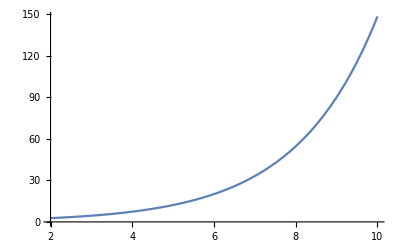

```mathematica
f[x_]:=ⅇ^(0.5x)
Plot[f[q],{q,2,10}]
```

```mathematica
a=4; (*начальное значения икса*)
b=8; (*конечное значения икса*)
h=0.001; (*шаг разбиений*)
n=Length@x-1; (*количество разбиений*)
x=Range[a,b,h]; (*таблица иксов*)
y=Table[f[x[[i]]],{i,1,Length@x}]; (*таблица значений*)
```

```mathematica
h(1/2 y[[1]]+1/2 y[[n]]+Sum[y[[i]],{i,2,n-1}])-h^4/180(f[b]^3-f[a]^3)-h^6/30240((f[b]^5-f[a]^5)) (*большая формула Симпсона*)
```

94.3636

```mathematica
Integrate[f[q],{q,4,8}] (*проверка встроенным оператором*)
```

94.4182